```mathematica
M2MD`MDExport[NotebookDirectory[]<>"123.md",EvaluationNotebook[]]
```

G:\GitHub Local Repository\Mathematica-Notebook-VersionControl\Folder\123.md

# 测试

## 普通计算

```mathematica
1+1
```

2

```mathematica
Sin[x+1]
```

Sin[1+x]

## 画图

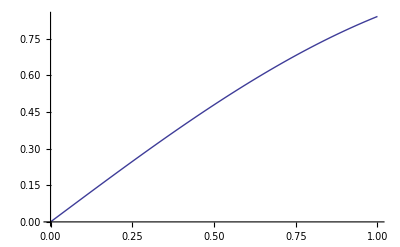

```mathematica
Plot[Sin[x],{x,0,1}]
```

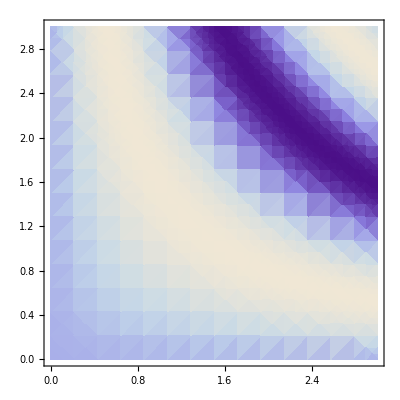

```mathematica
DensityPlot[Sin[x y],{x,0,3},{y,0,3}]
```

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3}]
```

-Graphics3D-

## 面板

```mathematica
class=Classify[{1->"A",2->"B"}]
```

ClassifierFunction[…]

```mathematica
class//Information
```

Classifier information
Data type | Numerical
Classes | ,,AB
Accuracy | (75.31.) %
Method | LogisticRegression
Single evaluation time | 2.03 ms/example
Batch evaluation speed | 181. examples/ms
Loss | 0.52 ± 0.17
Model memory | 176. kB
Training examples used | 2 examples
Training time | 847. ms

## 不同Cell

```mathematica
{{1,2},{3,4}}//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
{{1,2},{3,4}}//TeXForm
```

\left(
\begin{array}{cc}
 1 & 2 \\
 3 & 4 \\
\end{array}
\right)

```mathematica
<<M2MD`
```

```mathematica
MDExport["G:\\GitHub Local Repository\\Mathematica-Notebook-VersionControl\\nb2md-test\\exported.md",EvaluationNotebook[]]
```

G:\GitHub Local Repository\Mathematica-Notebook-VersionControl\nb2md-test\exported.md

```mathematica
$UserBaseDirectory
```

```mathematica
$ScriptCommandLine+1
```

```mathematica
NotebookGet
```